```mathematica
a := 7.7
b := -28.5
c := 44.8
d := -24
f[x_] := a*x+b*x^2+c*x^3+d*x^4
```

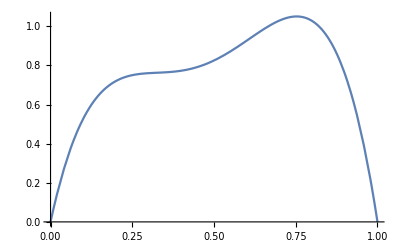

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
potential = DSolve[{y''[x]==1-f[x],y[0]==0,y[1]==0},y[x],x]
```

{{y[x]→-0.151667 x+0.5 x^2-1.28333 x^3+2.375 x^4-2.24 x^5+0.8 x^6}}

```mathematica
p[x_]=y[x]/.potential[[1]]
```

-0.151667 x+0.5 x^2-1.28333 x^3+2.375 x^4-2.24 x^5+0.8 x^6

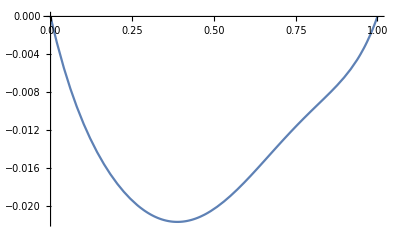

```mathematica
Plot[p[x],{x,0,1}]
```

```mathematica
alpha := 1.35
beta := 0.05
```

```mathematica
u[x_] := -alpha*p'[x]
```

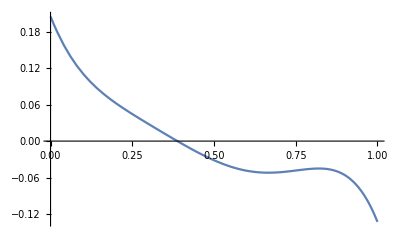

```mathematica
Plot[u[x],{x,0,1}]
```

```mathematica
F[x_] = u[x]*f'[x] - beta*f''[x]
```

-0.05 (-57.+268.8 x-288 x^2)-1.35 (7.7-57. x+134.4 x^2-96 x^3) (-0.151667+1. x-3.85 x^2+9.5 x^3-11.2 x^4+4.8 x^5)

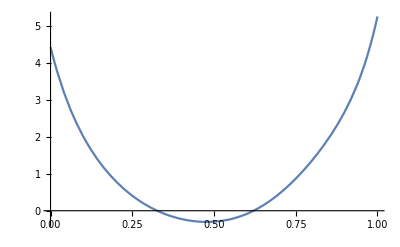

```mathematica
Plot[F[x],{x,0,1}]
```

```mathematica
Simplify[F[x]]
```

4.42658-35.5058 x+158.889 x^2-596.106 x^3+1675.59 x^4-3134.38 x^5+3632.69 x^6-2322.43 x^7+622.08 x^8

```mathematica
FortranForm[%]
```

4.426575000000002 - 35.50575000000001*x + 158.88915000000003*x**2 - 
     -  596.106*x**3 + 1675.5929999999998*x**4 - 3134.3759999999997*x**5 + 
     -  3632.687999999999*x**6 - 2322.4320000000002*x**7 + 622.0800000000002*x**8

```mathematica
FindMaximum[f[x],{x,0.8}]
```

{1.05007,{x→0.752836}}